```mathematica
(*Define constants of the problem*)
kBT=1.380649*10^(-23) * 200 * 10^-9;
a0=5.29*10^(-11);
hPlanck=6.62607015*10^(-34);
hbar=hPlanck/(2*Pi);
muNa40K=14.594251717637002*1.660538782*10^(-27);
ai=-1700 * a0;
af=640 * a0;
(*energies in units of kBT*)
Ei=hbar^2/(2*muNa40K*ai^2) / kBT;
Ef=hbar^2/(2*muNa40K*af^2) / kBT;
```

```mathematica
(*Lineshape from first-order calculation*)
```

```mathematica
pCOM=pNa+pK;
mu=mNa*mK/(mNa+mK);
pRel=(pNa/mNa-pK/mK)*mu;
mTot=mNa+mK;
```

```mathematica
pCOM^2/(2(mNa+mK))+pRel^2/(2*mu)//FullSimplify
```

1/2 (pK^2/mK+pNa^2/mNa)

```mathematica
T[w_,a_]:=1/(1/a - Sqrt[-w]);
```

```mathematica
f[x_]:=NIntegrate[P^2 *Exp[-P^2]*T[x-P^2,1],{P,0,100}];
```

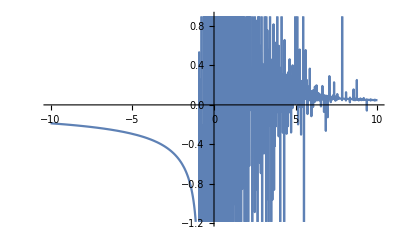

```mathematica
Plot[Re[f[x]],{x,-10,10}]
```

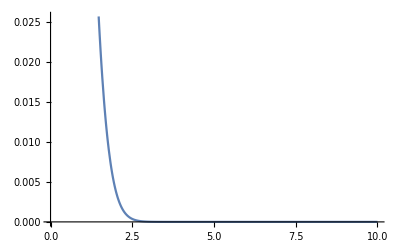

```mathematica
Plot[Exp[-(x^2-1)]/(10-(x^2/2-1-x^2)),{x,0,10}]
```

```mathematica
ComplexExpand[z/((x+I*y)-z)]
```

(x z)/(y^2+(x-z)^2)-(ⅈ y z)/(y^2+(x-z)^2)-z^2/(y^2+(x-z)^2)

```mathematica
Limit[(ⅈ y)/(y^2+(x-z)^2),{y->0}]
```

0

```mathematica
P**2*np.exp(-P**2)*4*(np.sqrt(x)/(x+Eb))/(En+0.005j-(-P**2/2+x))
```

```mathematica
F[En_]:=NIntegrate[(Sqrt[x]/(x+1))/(En+0.005*I - (x+1)),{x,0,100}]
```

```mathematica
Manipulate[Plot[Im[(Sqrt[x]/(x+1))/(En+eta*I- (x+1))],{x,0,2},PlotRange->Full],{En,-10,10},{eta,0,0.05}]
```

```mathematica
ComplexExpand[1/(En+0.005*I-(-P^2/2+1))]
```

-(1.+0.005 ⅈ)/(0.000025+(-1.+En+P^2/2)^2)+En/(0.000025+(-1.+En+P^2/2)^2)+P^2/(2 (0.000025+(-1.+En+P^2/2)^2))

```mathematica
Manipulate[Plot[-(Sqrt[x]/(x+1)) / (0.000025 +(-x+1+En)^2 ),{x,0,2.0},PlotRange->Full],{En,-10,10}]
```